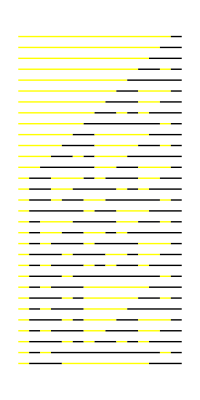

-Graphics-

```mathematica
list = Table[0, {30}];
list[[15]] = 1;
rules = {
{0,0,0} -> 0,
{0,0,1} -> 1, 
{0,1,0} -> 1, 
{0,1,1} -> 1, 
{1,0,0} -> 0, 
{1,0,1} -> 1,
{1,1,0} -> 1,
{1,1,1} -> 0
};
(*Chop up the list and apply the rules*)
Partition[list, 3, 1] /. rules;
(*Pad the list with zeros on both sides*)
Join[{0}, list, {0}];
(*Create a function to do this*)
step[seq_] := Join[{0}, Partition[seq, 3, 1] /. rules, {0}];
array = NestList[step, list, 30];

summarizedArray = {};

For[i = 1, i≤ Length[array], ++i,
	(* row i *)
	line = {};
	For[j=1, j≤ Length[array[[i]]], ++j,
		If[Length[line] == 0, (* init *)
			line = {i,j,i,j, array[[i,j]]}, 
		(*else: if value is the same as last line's value*)
			If[array[[i,j]] == line[[5]],
				line = {line[[1]], line[[2]], i,j, line[[5]]},
				(*else: new value --> store old line, start new line*)
				summarizedArray = Append[summarizedArray, line]; line = {i,j,i,j,array[[i,j]]}]
		]
	]
]
SubArrayToLine[a_] := (
	p1 = {a[[2]]-0.5, -a[[1]]};
	p2 = {a[[4]]+0.5, -a[[3]]};
	l = Line[{p1, p2}];
	Return[l];
)
FormattingOfLine[x_]:=(
	Return[
		If[x == 0 , Yellow, Black]
	];
)

properLines = {};
For[k = 1, k ≤ Length[summarizedArray],++k,
	properLines = Append[properLines, FormattingOfLine[summarizedArray[[k,5]]]];
	properLines = Append[properLines, SubArrayToLine[lines[[k]]]];
]

Graphics[{
	Thick,
	(*formattedLines*)
	properLines
}]

ArrayPlot[array]
```